## First Solution(dimensionless)

```mathematica
Vi[n_, i_] :=Vi[n, i]=(-1)^(i + n/2) Sum[ k^(n/2) (2 k)! /( (n/2 - k)! k! (k - 1)! (i - k)! (2 k - i)! ), { k, Floor[ (i+1)/2 ], Min[ i, n/2] } ] //N;Stehfest[F_, s_, t_, n_:16] :=
Log[2]/t Sum[ Vi[n, i]*F /. s -> i Log[2]/t , {i, 1, n} ]  //N;s1r=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 ((Cr p+β) √(p+κ ξ^2) Cosh[√(p+κ ξ^2)]+Cr p β Sinh[√(p+κ ξ^2)]))/(p (β (p+κ ξ^2)+Cr p (p+κ ξ^2+β √(p+κ ξ^2)))) (Cosh[x η]-Sinh[x η]),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;s1l=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 ((Cr p+β) √(p+κ ξ^2) Cosh[x √(p+κ ξ^2)]+Cr p β Sinh[x √(p+κ ξ^2)]))/(p (β (p+κ ξ^2)+Cr p (p+κ ξ^2+β √(p+κ ξ^2))) (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;Q=Compile[{{t,_Real}},2/Pi*2*NIntegrate[Stehfest[Cr*p*((2 β (Cr p+β) √(p+κ ξ^2))/(Cr p (p+β/Cr) (β (p+κ ξ^2)+Cr p (p+κ ξ^2+β √(p+κ ξ^2))) (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]))),p,t,6]*Cos[y ξ],{ξ,0,∞},{y,0,3.07*√t},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;
H=Compile[{{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 β (Cr p+β) √(p+κ ξ^2))/(Cr p (p+β/Cr) (β (p+κ ξ^2)+Cr p (p+κ ξ^2+β √(p+κ ξ^2))) (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;
s[x_,y_,t_]:=If[0<x<1,s1l[x,y,t],s1r[x,y,t]]//Quiet;
β=10;(*Subscript[β, D]*)
Cr=25;(*Subscript[C, rD]*)
κ=1;(*Subscript[K, y]/Subscript[K, x]*)
(*Q(t) for dimensionless stream depletion*)
(*H(y,t) for dimensionless stream drawdown*)(*s(x,y,t) for dimensionless aquifer drawdown*)
```

Example

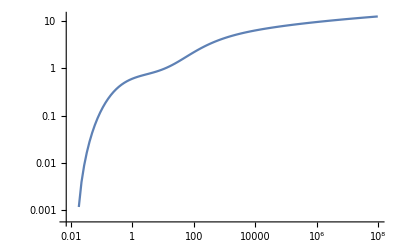

```mathematica
ListLogLogPlot[{#,s[0.5,0.1,#]}&/@Exp@N@Range[Log[0.01],Log@(10^8),1/5],Joined->True]
```

## Second Solution(dimensionless)

```mathematica
s1r=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 (Cosh[x √(p+κ ξ^2)]-Sinh[x √(p+κ ξ^2)]) ((Cr p+β) Cosh[√(p+κ ξ^2)] (√(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(p+κ ξ^2) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])+Sinh[√(p+κ ξ^2)] ((Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(β (p+κ ξ^2)+Cr p (p+β+κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])))/(2 p (Cr p+β) (p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+p √(p+κ ξ^2) (2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;s1l=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 ((Cr p+β) Cosh[x √(p+κ ξ^2)] (√(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(p+κ ξ^2) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])+Sinh[x √(p+κ ξ^2)] ((Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(β (p+κ ξ^2)+Cr p (p+β+κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])))/(p √(p+κ ξ^2) (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]) (2 (Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;s2=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 (Cr p+β) (√(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[(W+x) √(p+β-β^2/(Cr p+β)+κ ξ^2)]+√(p+κ ξ^2) Sinh[(W+x) √(p+β-β^2/(Cr p+β)+κ ξ^2)]))/(p (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]) (2 (Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;s3=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 (Cr p+β) √(p+β-β^2/(Cr p+β)+κ ξ^2) (Cosh[W √(p+κ ξ^2)]+Sinh[W √(p+κ ξ^2)]) (Cosh[x √(p+κ ξ^2)]+Sinh[x √(p+κ ξ^2)]))/(p (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]) (2 (Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;
H=Compile[{{x,_Real},{y,_Real},{t,_Real}},2/Pi*NIntegrate[Re[Stehfest[(2 β (√(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[(W+x) √(p+β-β^2/(Cr p+β)+κ ξ^2)]+√(p+κ ξ^2) Sinh[(W+x) √(p+β-β^2/(Cr p+β)+κ ξ^2)]))/(p (Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]) (2 (Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])),p,t,6]]*Cos[y ξ],{ξ,0,∞},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;Q=Compile[{{t,_Real}},2/Pi*2*NIntegrate[Stehfest[(2 Cr β ((√(p+κ ξ^2) (-1+Cosh[W √((p (β+Cr (p+β)))/(Cr p+β)+κ ξ^2)]))/(√((p (β+Cr (p+β)))/(Cr p+β)+κ ξ^2))+Sinh[W √((p (β+Cr (p+β)))/(Cr p+β)+κ ξ^2)]))/((Cosh[√(p+κ ξ^2)]+Sinh[√(p+κ ξ^2)]) (2 (Cr p+β) √(p+κ ξ^2) √(p+β-β^2/(Cr p+β)+κ ξ^2) Cosh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)]+(2 β (p+κ ξ^2)+Cr p (2 p+β+2 κ ξ^2)) Sinh[W √(p+β-β^2/(Cr p+β)+κ ξ^2)])),p,t,6]*Cos[y ξ],{ξ,0,∞},{y,0,3.07*√t},Method->{"LevinRule","LevinFunctions"->{Exp,Sin,Cos}},AccuracyGoal->20,MaxRecursion->40],RuntimeOptions->"EvaluateSymbolically"->False,RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"]//Quiet;s[x_,y_,t_]:=If[x<-W,s3[x,y,t],If[-W<x<0,s2[x,y,t],If[0<x<1,s1l[x,y,t],s1r[x,y,t]]]]//Quiet;
β=10;(*Subscript[β, D]*)
Cr=25;(*Subscript[C, rD]*)
κ=1;(*Subscript[K, y]/Subscript[K, x]*)
W=10;(*Subscript[W, D]*)
(*Q(t) for dimensionless stream depletion*)
(*H(x,y,t) for dimensionless stream drawdown*)(*s(x,y,t) for dimensionless aquifer drawdown*)
```

Example

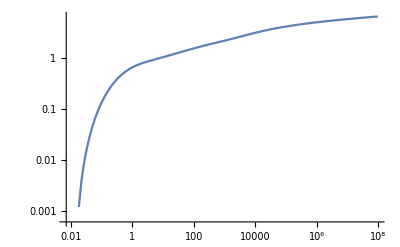

```mathematica
ListLogLogPlot[{#,s[0.5,0.1,#]}&/@Exp@N@Range[Log[0.01],Log@(10^8),1/5],Joined->True]
```